```mathematica
a=-1;
b=1;
n=512;
h=(b-a)/n;
x={};
y={};
f[x_]:=x;

For[i=0,i<n+1,i++,
xi=a+i*h;
AppendTo[x,N@xi];
AppendTo[y,N[f[xi]]];
]

n1=2;
h1=(b-a)/n1;
x1={};
y1={};
f[x_]:=x;

For[i=0,i<n1+1,i++,
xi=a+i*h1;
AppendTo[x1,N@xi];
AppendTo[y1,N[f[xi]]];
]
```

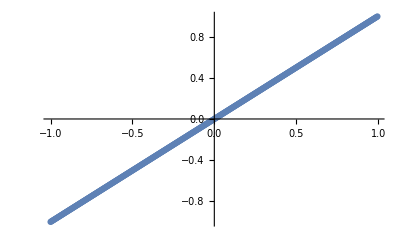

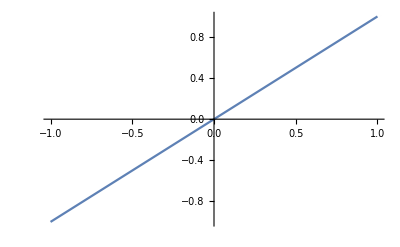

```mathematica
Lagr[n_]:=Module[
{a=-1,b=1},
x={};
y={};

h=(b-a)/n;
x={};
y={};
f[x_]:=x;

For[i=0,i<n+1,i++,
xi=a+i*h;
AppendTo[x,N@xi];
AppendTo[y,N[f[xi]]];
]
Return[x,y];
];



ListPlot[Table[{x[[i]],y[[i]]},{i,512}]]

k=InterpolatingPolynomial[{{x1[[1]],y1[[1]]},{x1[[2]],y1[[2]]},{x1[[3]],y1[[3]]}},z];
Plot[k,{z,-1,1}]
```

```mathematica
Lagr[0.5]
```

Return[0]

1.47819

1

0

```mathematica
k=InterpolatingPolynomial[{{x[[1]],y[[1]]},{x[[2]],y[[2]]},{x[[3]],y[[3]]},{x[[4]],y[[4]]},{x[[5]],y[[5]]},{x[[6]],y[[6]]}},z]
```

1.48014+(1.+z) (0.+(-1.+z) (0.551656+(0.2+z) (-0.448553+(-0.6+z) (-1.12138+1.85037×10^-16 (0.6+z)))))

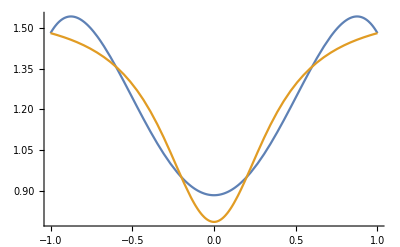

```mathematica
Plot[{k,ArcTan[1+10*z^2]},{z,-1,1}]
```